```mathematica
myAxesSize=21;
myLabelSize=18;
myImageSize=1000;
SetDirectory[NotebookDirectory[]];
h={1,1/2,1/4,1/8,1/16};
```

## Poisson 0.3

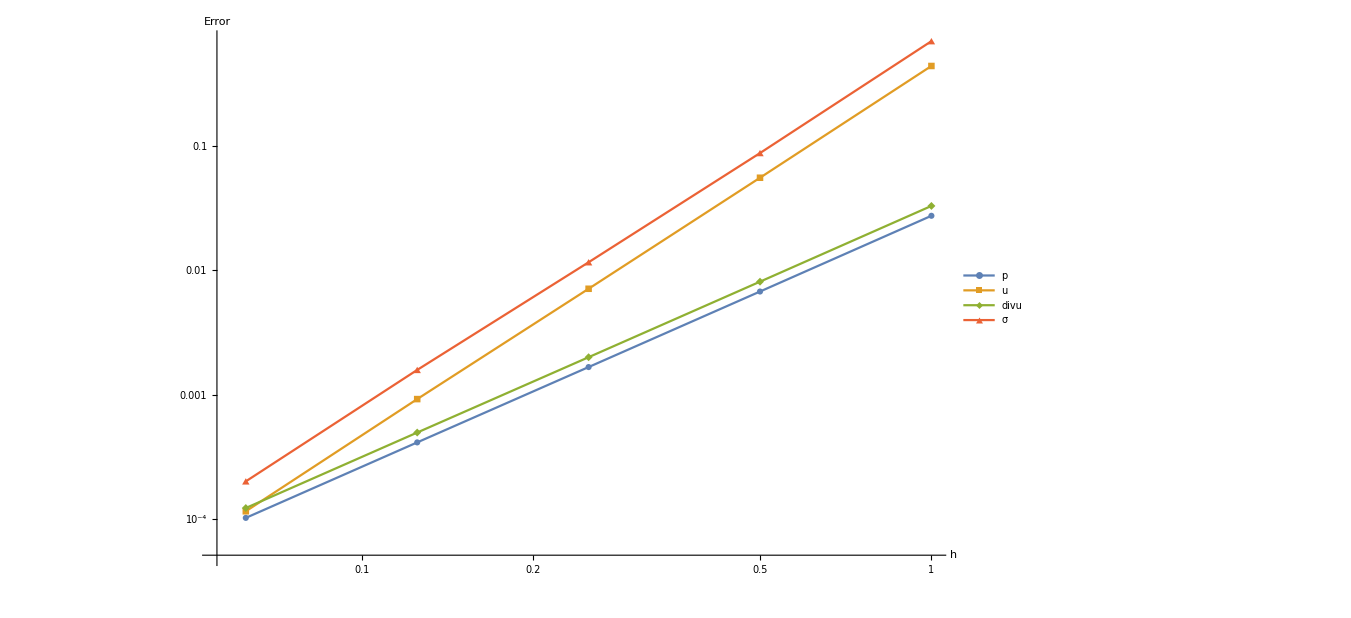

{2.02159,2.01619,2.01066,2.01477}

{2.98308,2.96328,2.94472,2.99408}

{2.02159,2.01618,2.01067,2.01478}

{2.98644,2.91442,2.87367,2.97438}

```mathematica
(*poisson=0.3*)
Errors1={0.027508,0.62113,0.439653,532.949,0.0330096,0.745356,0.695611,65.7889};
Errors2={0.00677487,0.62113,0.055605,524.069,0.00812985,0.745356,0.0877727,57.3788};
Errors3={0.00167482,0.62113,0.00712983,521.84,0.00200979,0.745356,0.0116421,55.0652};
Errors4={0.000415622,0.62113,0.000926043,521.285,0.000498746,0.745356,0.00158844,54.4707};
Errors5={0.000102847,0.62113,0.000116231,521.148,0.000123416,0.745356,0.000202112,54.3211};
Err={Errors1,Errors2,Errors3,Errors4,Errors5};

perr=Table[{h[[i]],Err[[i,1]]},{i,Length[Err]}];
uerr=Table[{h[[i]],Err[[i,3]]},{i,Length[Err]}];
divuerr=Table[{h[[i]],Err[[i,5]]},{i,Length[Err]}];
sigmaerr=Table[{h[[i]],Err[[i,7]]},{i,Length[Err]}];
ListLogLogPlot[{perr,uerr,divuerr,sigmaerr},Joined->True,PlotMarkers->Automatic,ImageSize->myImageSize,AxesLabel->{Style["h",myAxesSize,Black],Style["Error",myAxesSize,Black]},LabelStyle->Directive[myLabelSize*1.2,Bold,Black],PlotLegends->Placed[LineLegend[{"p","u","divu","σ"},LegendFunction->(Framed[#1, FrameMargins -> 0,Background->White] & )],{0.2,0.75}],GridLines->Automatic]

Table[Log[perr[[i,2]]/perr[[i+1,2]]]/Log[2],{i,1,Length[uerr]-1}]
Table[Log[uerr[[i,2]]/uerr[[i+1,2]]]/Log[2],{i,1,Length[uerr]-1}]
Table[Log[divuerr[[i,2]]/divuerr[[i+1,2]]]/Log[2],{i,1,Length[divuerr]-1}]
Table[Log[sigmaerr[[i,2]]/sigmaerr[[i+1,2]]]/Log[2],{i,1,Length[sigmaerr]-1}]
```

## Poisson 0.49

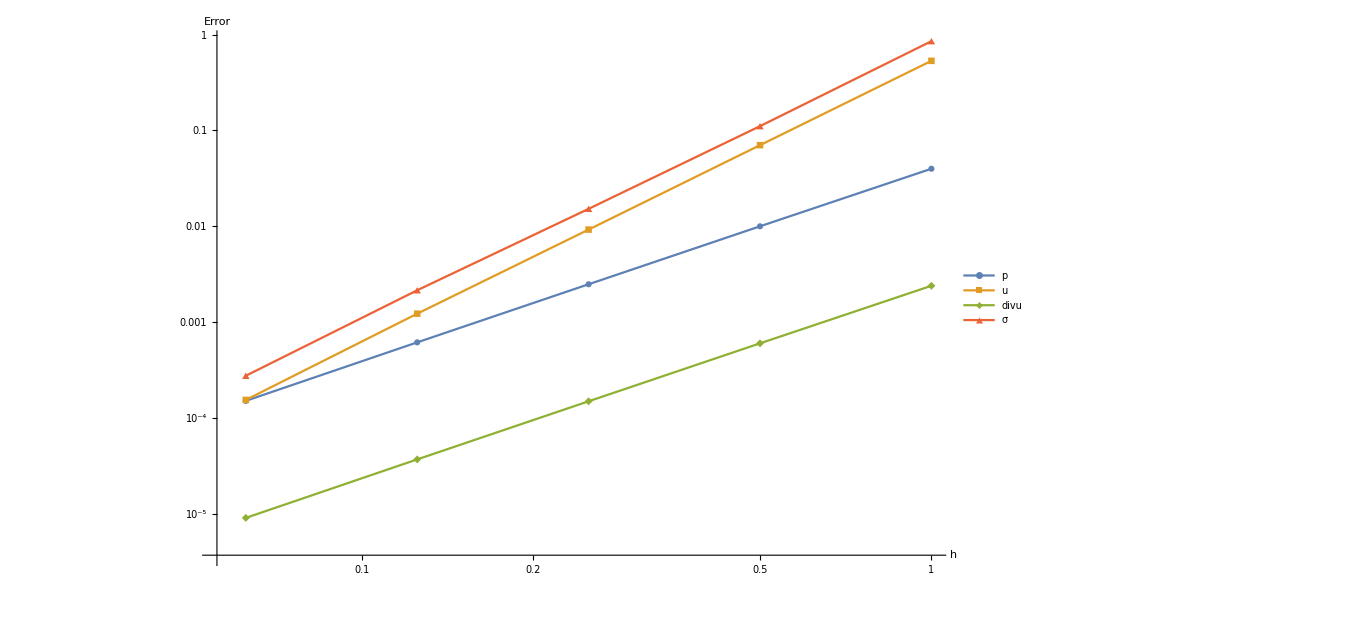

{1.99607,2.0096,2.01531,2.02814}

{2.92473,2.92751,2.9164,2.99026}

{1.99607,2.0096,2.01531,2.02815}

{2.94714,2.86768,2.82381,2.96489}

```mathematica
(*poisson=0.49*)
Errors1={0.0398614,0.62113,0.533428,532.662,0.00239168,0.0372678,0.855673,65.8037};
Errors2={0.00999256,0.62113,0.0702496,524.115,0.000599553,0.0372678,0.110951,57.387};
Errors3={0.00248157,0.62113,0.00923371,521.967,0.000148894,0.0372678,0.0152011,55.0692};
Errors4={0.000613843,0.62113,0.00122307,521.431,3.68306 10^-05,0.0372678,0.00214696,54.4733};
Errors5={0.000150496,0.62113,0.000153919,521.299,9.02973 10^-06,0.0372678,0.000274982,54.3232};
Err={Errors1,Errors2,Errors3,Errors4,Errors5};

perr=Table[{h[[i]],Err[[i,1]]},{i,Length[Err]}];
uerr=Table[{h[[i]],Err[[i,3]]},{i,Length[Err]}];
divuerr=Table[{h[[i]],Err[[i,5]]},{i,Length[Err]}];
sigmaerr=Table[{h[[i]],Err[[i,7]]},{i,Length[Err]}];
ListLogLogPlot[{perr,uerr,divuerr,sigmaerr},Joined->True,PlotMarkers->Automatic,ImageSize->myImageSize,AxesLabel->{Style["h",myAxesSize,Black],Style["Error",myAxesSize,Black]},LabelStyle->Directive[myLabelSize*1.2,Bold,Black],PlotLegends->Placed[LineLegend[{"p","u","divu","σ"},LegendFunction->(Framed[#1, FrameMargins -> 0,Background->White] & )],{0.2,0.75}],GridLines->Automatic]

Table[Log[perr[[i,2]]/perr[[i+1,2]]]/Log[2],{i,1,Length[uerr]-1}]
Table[Log[uerr[[i,2]]/uerr[[i+1,2]]]/Log[2],{i,1,Length[uerr]-1}]
Table[Log[divuerr[[i,2]]/divuerr[[i+1,2]]]/Log[2],{i,1,Length[divuerr]-1}]
Table[Log[sigmaerr[[i,2]]/sigmaerr[[i+1,2]]]/Log[2],{i,1,Length[sigmaerr]-1}]
```

## Poisson 0.4999

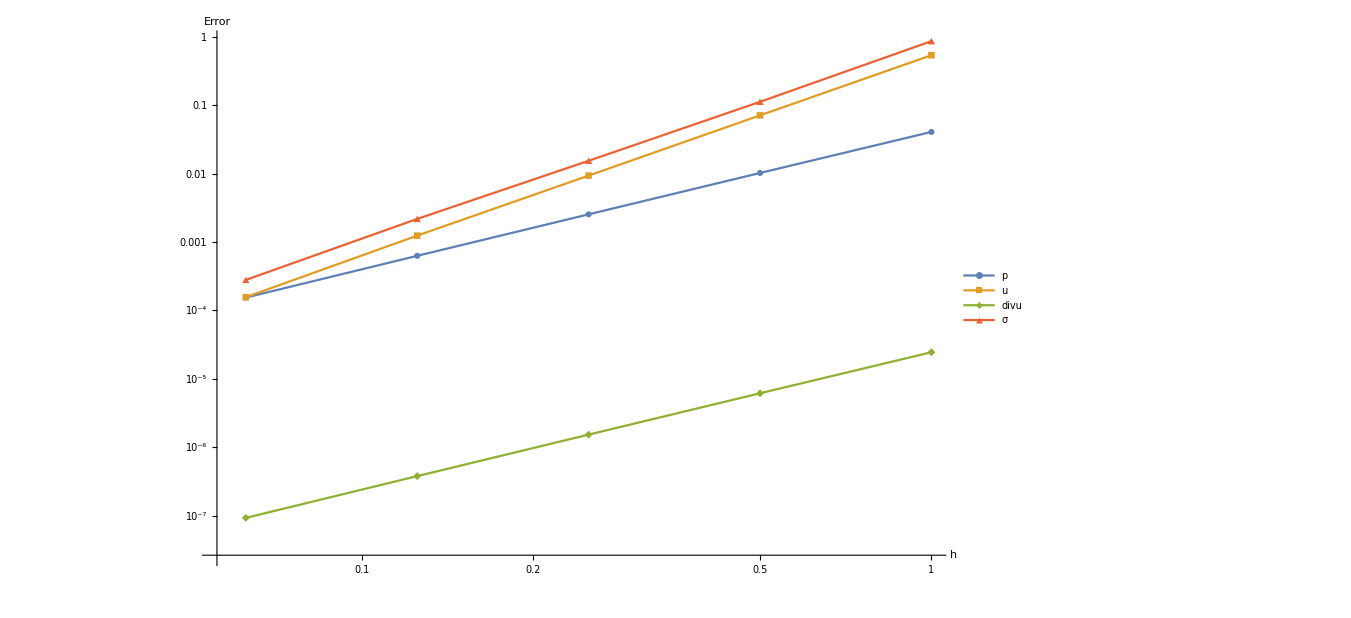

{1.99425,2.0092,2.01577,2.02912}

{2.92187,2.92621,2.916,2.99027}

{1.99425,2.00921,2.01576,2.02913}

{2.94558,2.86635,2.82298,2.96452}

```mathematica
(*poisson=0.4999*)
Errors1={0.0408293,0.62113,0.54037,532.649,2.44976 10^-05,0.000372678,0.867383,65.8044};
Errors2={0.0102481,0.62113,0.0713051,524.119,6.14887 10^-06,0.000372678,0.112591,57.3874};
Errors3={0.00254574,0.62113,0.00938085,521.974,1.52744 10^-06,0.000372678,0.01544,55.0694};
Errors4={0.000629517,0.62113,0.00124291,521.44,3.7771 10^-07,0.000372678,0.00218196,54.4734};
Errors5={0.000154234,0.62113,0.000156415,521.308,9.25402 10^-08,0.000372678,0.000279536,54.3234};
Err={Errors1,Errors2,Errors3,Errors4,Errors5};

perr=Table[{h[[i]],Err[[i,1]]},{i,Length[Err]}];
uerr=Table[{h[[i]],Err[[i,3]]},{i,Length[Err]}];
divuerr=Table[{h[[i]],Err[[i,5]]},{i,Length[Err]}];
sigmaerr=Table[{h[[i]],Err[[i,7]]},{i,Length[Err]}];
ListLogLogPlot[{perr,uerr,divuerr,sigmaerr},Joined->True,PlotMarkers->Automatic,ImageSize->myImageSize,AxesLabel->{Style["h",myAxesSize,Black],Style["Error",myAxesSize,Black]},LabelStyle->Directive[myLabelSize*1.2,Bold,Black],PlotLegends->Placed[LineLegend[{"p","u","divu","σ"},LegendFunction->(Framed[#1, FrameMargins -> 0,Background->White] & )],{0.2,0.75}],GridLines->Automatic]

Table[Log[perr[[i,2]]/perr[[i+1,2]]]/Log[2],{i,1,Length[uerr]-1}]
Table[Log[uerr[[i,2]]/uerr[[i+1,2]]]/Log[2],{i,1,Length[uerr]-1}]
Table[Log[divuerr[[i,2]]/divuerr[[i+1,2]]]/Log[2],{i,1,Length[divuerr]-1}]
Table[Log[sigmaerr[[i,2]]/sigmaerr[[i+1,2]]]/Log[2],{i,1,Length[sigmaerr]-1}]
```

## Poisson 0.499999

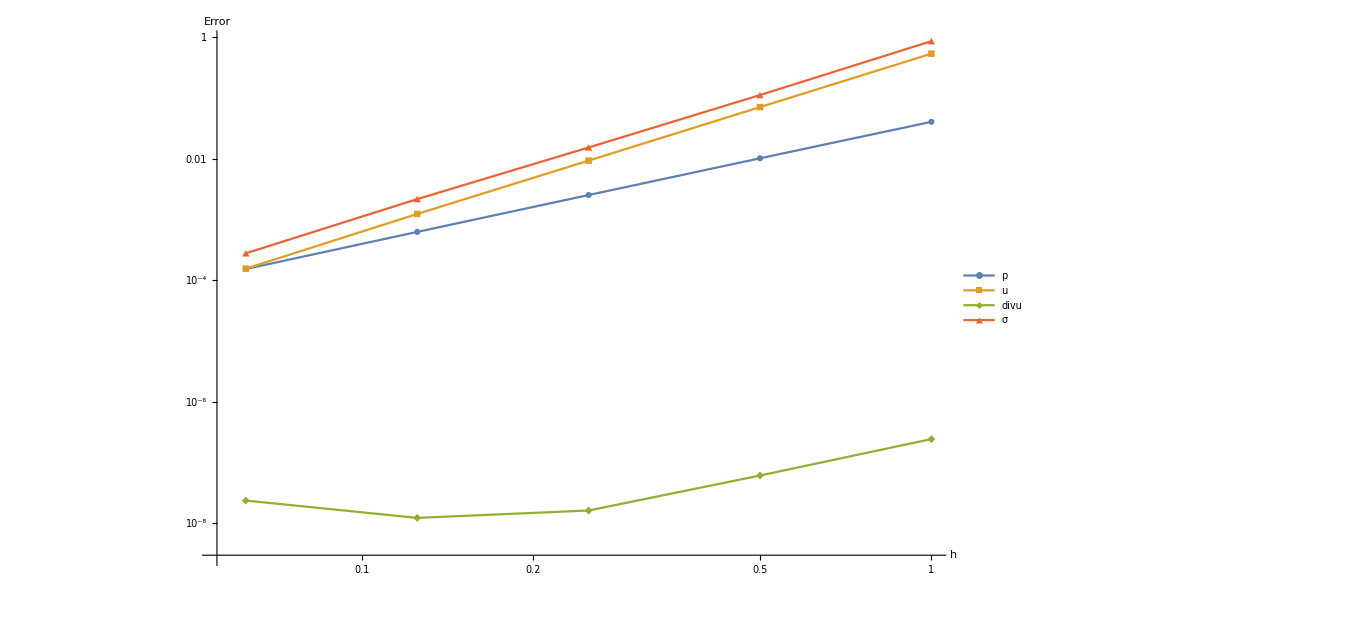

{1.99424,2.00919,2.01577,2.02914}

{2.92184,2.9262,2.916,2.99026}

{1.99295,1.91292,0.403299,-0.946499}

{2.94557,2.86633,2.82297,2.96451}

```mathematica
(*poisson=0.499999*)
Errors1={0.0408393,0.62113,0.540441,532.648,2.45068 10^-07,3.72678 10^-06,0.867502,65.8044};
Errors2={0.0102507,0.62113,0.0713159,524.119,6.15672 10^-08,3.72678 10^-06,0.112607,57.3874};
Errors3={0.0025464,0.62113,0.00938235,521.974,1.63495 10^-08,3.72678 10^-06,0.0154424,55.0694};
Errors4={0.000629678,0.62113,0.00124311,521.44,1.23623 10^-08,3.72678 10^-06,0.00218231,54.4734};
Errors5={0.000154272,0.62113,0.000156441,521.308,2.38245 10^-08,3.72678 10^-06,0.000279583,54.3234};
Err={Errors1,Errors2,Errors3,Errors4,Errors5};

perr=Table[{h[[i]],Err[[i,1]]},{i,Length[Err]}];
uerr=Table[{h[[i]],Err[[i,3]]},{i,Length[Err]}];
divuerr=Table[{h[[i]],Err[[i,5]]},{i,Length[Err]}];
sigmaerr=Table[{h[[i]],Err[[i,7]]},{i,Length[Err]}];
ListLogLogPlot[{perr,uerr,divuerr,sigmaerr},Joined->True,PlotMarkers->Automatic,ImageSize->myImageSize,AxesLabel->{Style["h",myAxesSize,Black],Style["Error",myAxesSize,Black]},LabelStyle->Directive[myLabelSize*1.2,Bold,Black],PlotLegends->Placed[LineLegend[{"p","u","divu","σ"},LegendFunction->(Framed[#1, FrameMargins -> 0,Background->White] & )],{0.2,0.75}],GridLines->Automatic]

Table[Log[perr[[i,2]]/perr[[i+1,2]]]/Log[2],{i,1,Length[uerr]-1}]
Table[Log[uerr[[i,2]]/uerr[[i+1,2]]]/Log[2],{i,1,Length[uerr]-1}]
Table[Log[divuerr[[i,2]]/divuerr[[i+1,2]]]/Log[2],{i,1,Length[divuerr]-1}]
Table[Log[sigmaerr[[i,2]]/sigmaerr[[i+1,2]]]/Log[2],{i,1,Length[sigmaerr]-1}]
```

## Poisson 0.5

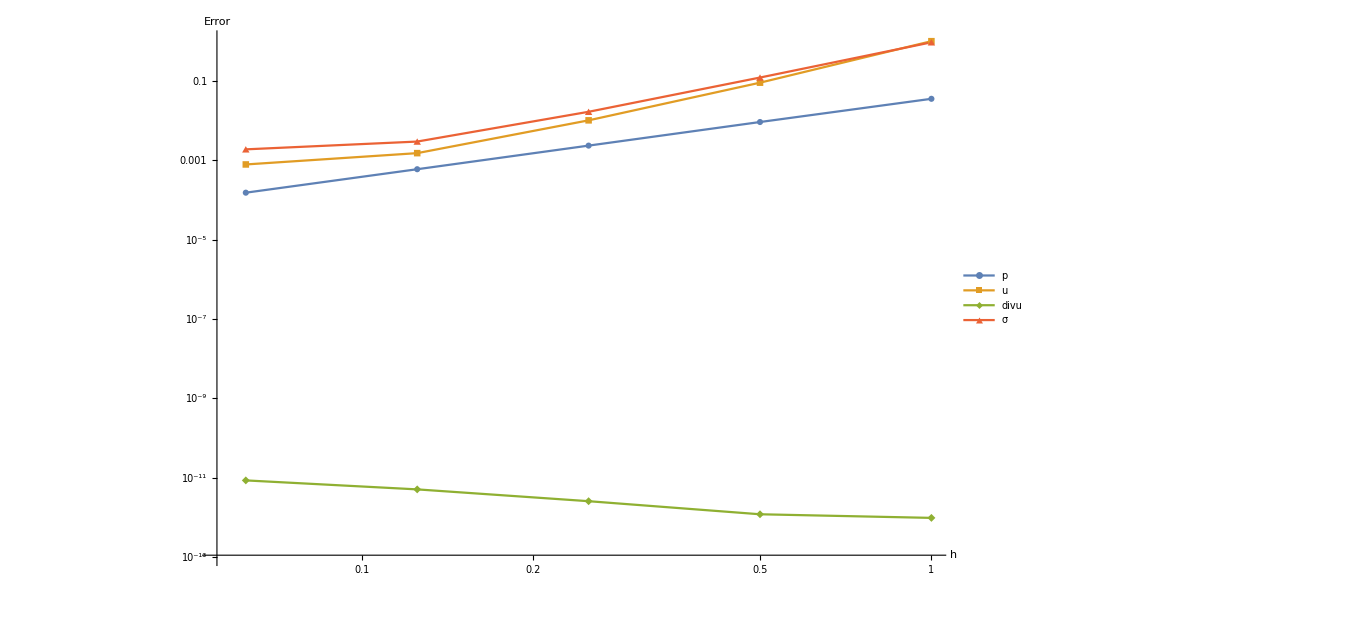

{1.94583,1.97725,1.97858,1.96609}

{3.47824,3.15601,2.74873,0.948138}

{-0.302668,-1.09602,-0.989468,-0.752936}

{2.95154,2.86966,2.49518,0.652718}

```mathematica
(*poisson=0.5*)
Errors1={0.0358433,0.62113,1.0187,532.648,9.5916 10^-13,0,0.953072,169.377};
Errors2={0.00930367,0.62113,0.0914099,524.119,1.18305 10^-12,0,0.123204,147.463};
Errors3={0.00236288,0.62113,0.0102551,521.974,2.52893 10^-12,0,0.0168567,141.469};
Errors4={0.000599556,0.62113,0.00152577,521.44,5.02107 10^-12,0,0.00298984,139.932};
Errors5={0.000153454,0.62113,0.000790808,521.308,8.4616 10^-12,0,0.00190178,139.545};
Err={Errors1,Errors2,Errors3,Errors4,Errors5};

perr=Table[{h[[i]],Err[[i,1]]},{i,Length[Err]}];
uerr=Table[{h[[i]],Err[[i,3]]},{i,Length[Err]}];
divuerr=Table[{h[[i]],Err[[i,5]]},{i,Length[Err]}];
sigmaerr=Table[{h[[i]],Err[[i,7]]},{i,Length[Err]}];
ListLogLogPlot[{perr,uerr,divuerr,sigmaerr},Joined->True,PlotMarkers->Automatic,ImageSize->myImageSize,AxesLabel->{Style["h",myAxesSize,Black],Style["Error",myAxesSize,Black]},LabelStyle->Directive[myLabelSize*1.2,Bold,Black],PlotLegends->Placed[LineLegend[{"p","u","divu","σ"},LegendFunction->(Framed[#1, FrameMargins -> 0,Background->White] & )],{0.2,0.75}],GridLines->Automatic]

Table[Log[perr[[i,2]]/perr[[i+1,2]]]/Log[2],{i,1,Length[uerr]-1}]
Table[Log[uerr[[i,2]]/uerr[[i+1,2]]]/Log[2],{i,1,Length[uerr]-1}]
Table[Log[divuerr[[i,2]]/divuerr[[i+1,2]]]/Log[2],{i,1,Length[divuerr]-1}]
Table[Log[sigmaerr[[i,2]]/sigmaerr[[i+1,2]]]/Log[2],{i,1,Length[sigmaerr]-1}]
```